```mathematica
ClearAll["Global`*"];
```

```mathematica
(* Constants *)
hbar = (6.626 10^-34)/(2 π);
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
B0 = 513 *10^-14 (* DC Applied field [T] *);
ωs=hbar (-γe B0)/(2π);
ωI=hbar(γN B0)/(2π);
Ahf = -2.16*10^6 hbar; (* Hyperfine interaction [s^-1] *)
Dzfs = 2870*10^6 hbar; (* Zero-field-splitting for electron triplet [s^-1] *)
Pzfs = -4.95*10^6 hbar; (* Zero-field-splitting for^14 N [s^-1] *)
```

```mathematica
(* Triplet spin operators *)

Sz = { {1, 0}, {0, 0} };
Sy = 1/(Sqrt[2] I) { {0, 1}, {-1, 0}};
Sx =1/Sqrt[2] { {0, 1}, {1, 0} };
eye2 = { {1, 0}, {0, 1} };

(* Electron triplet operators *)

eSx = KroneckerProduct[Sx, eye2];
eSz = KroneckerProduct[Sz, eye2];

(* N14 operators *)

Iz = KroneckerProduct[eye2, Sz];

(* Simulation parameters *)

pulseAmplitude = hbar;
pulsePhase = 0;

tStart = 0;
tEnd = 2.38892550438441*^-10;
freqStart = 0.1*10^3;
freqEnd = 10*10^3;
freqStep = 100;
```

```mathematica
KroneckerProduct[{ {a11, a12},{a21,a22}} , { {b11, b12}, {b21, b22}}] //MatrixForm
```

(a11 b11 | a11 b12 | a12 b11 | a12 b12
a11 b21 | a11 b22 | a12 b21 | a12 b22
a21 b11 | a21 b12 | a22 b11 | a22 b12
a21 b21 | a21 b22 | a22 b21 | a22 b22)

```mathematica
Eigenvalues[Subscript[H, NV]]
```

{1.90166×10^-24,1.89815×10^-24,-3.27987×10^-27,0.}

```mathematica
(* Define Hamiltonian *)

Subscript[H, hf]=  Ahf eSz . Iz; (* Secular approximation *)
Subscript[H, NV] = 2π ( Dzfs eSz.eSz  + ωs eSz + Pzfs  Iz.Iz - ωI Iz) + Subscript[H, hf];
Hc[t_]:= pulseAmplitude Sin[ 2π f t + pulsePhase ] eSx 
H[t_] := Subscript[H, NV]
H[t_] := Subscript[H, NV]+ Hc[t]
```

```mathematica
(* Define density matrix *)

density = Table[ ρ[i, j][t],{i, 1, 4}, {j, 1, 4}];
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, 4}, {j, i+1, 4}];

density // MatrixForm
```

(ρ[1,1][t] | ρ[1,2][t] | ρ[1,3][t] | ρ[1,4][t]
Conjugate[ρ[1,2][t]] | ρ[2,2][t] | ρ[2,3][t] | ρ[2,4][t]
Conjugate[ρ[1,3][t]] | Conjugate[ρ[2,3][t]] | ρ[3,3][t] | ρ[3,4][t]
Conjugate[ρ[1,4][t]] | Conjugate[ρ[2,4][t]] | Conjugate[ρ[3,4][t]] | ρ[4,4][t])

```mathematica
(* Define initial value of density matrix *)

density0 = Table[
ρ[i, j][0] == If[ i ==1 && j == 2, 1, 0]
, {i, 1, 4}, {j, i, 4}] // Flatten;
```

```mathematica
(* Define master equation *)

eqnTotal = ⅈ  D[ density, t] - (H[t].density - density.H[t]) // Simplify;
eqns = Table[ eqnTotal[[i, j]],  {i, 1, 4}, {j, i, 4}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, 4}, {j, i, 4}] // Flatten;
```

```mathematica
(* Solve equation for different frequencies *)

simdata = {};

Do[
params = { diffeqs /. f -> freq, density0 } //Flatten;
sol = NDSolve[ params, funcs, {t,tStart, tEnd}]; 

prob = 1/(tEnd-tStart)NIntegrate[ Abs[ρ[1,1][t] /. sol], {t, tStart, tEnd}];
AppendTo[simdata, ρ[1,2][t] /. sol];

, {freq, freqStart, freqEnd, freqStep}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

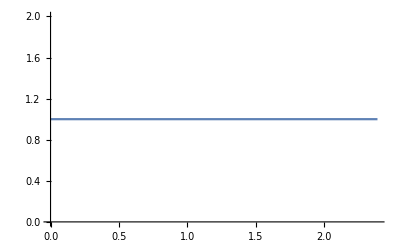

```mathematica
Plot[ simdata[[1]] ,{t, 0, tEnd}]
```

```mathematica
x[t] = ρ[1,2][t] /. NDSolve[{params[[2]], ρ[1,2][0] == 2}, ρ[1,2][t], {t, 0, 1}][[1]]
Plot[Abs[x[t]], {t, 0, 1}]
```

NDSolve::underdet: There are more dependent variables, {ρ[1,2][t],ρ[1,4][t],ρ[2,3][t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {-7.45687×10^-35 Conjugate[ρ[2,3][t]] Sin[62831.9 t]+3.50766×10^-27 ρ[1,2][t]+7.45687×10^-35 Sin[62831.9 t] ρ[1,4][t]+ⅈ ρ[1,2]'[t]==0,ρ[1,2][0]==2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ρ[1,2][t]/.{-7.45687×10^-35 Conjugate[ρ[2,3][t]] Sin[62831.9 t]+3.50766×10^-27 ρ[1,2][t]+7.45687×10^-35 Sin[62831.9 t] ρ[1,4][t]+ⅈ ρ[1,2]'[t]==0,ρ[1,2][0]==2}

ReplaceAll::reps: {-7.15138×10^-35 Conjugate[ρ[2,3][0.0000204286]]+3.50766×10^-27 ρ[1,2][0.0000204286]+7.15138×10^-35 ρ[1,4][0.0000204286]+ⅈ ρ[1,2]'[0.0000204286]==0,ρ[1,2][0]==2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-7.15138×10^-35 Conjugate[ρ[2.,3.][0.0000204286]]+3.50766×10^-27 ρ[1.,2.][0.0000204286]+7.15138×10^-35 ρ[1.,4.][0.0000204286]+(0.+1. ⅈ) ρ[1.,2.]'[0.0000204286]==0.,ρ[1.,2.][0.]==2.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-7.26778×10^-35 Conjugate[ρ[2,3][0.0204286]]+3.50766×10^-27 ρ[1,2][0.0204286]+7.26778×10^-35 ρ[1,4][0.0204286]+ⅈ ρ[1,2]'[0.0204286]==0,ρ[1,2][0]==2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
params[[2]]
```

-7.45687×10^-35 Conjugate[ρ[2,3][t]] Sin[62831.9 t]+3.50766×10^-27 ρ[1,2][t]+7.45687×10^-35 Sin[62831.9 t] ρ[1,4][t]+ⅈ ρ[1,2]'[t]==0

```mathematica
DSolve[{params[[2]], ρ[1,2][0] == 2}, ρ[1,2][t], t][[1]]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

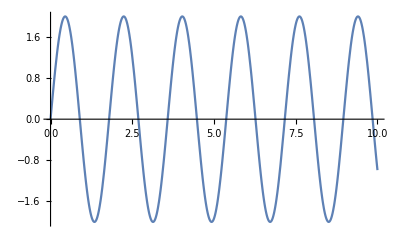

```mathematica
Plot[Im[2. ⅇ^((0.+3.507655101043101 ⅈ) t)], {t, 0, 10}]
```